```mathematica
(*Definição das novas coordenadas*)x={(R+r Cos[ψ]) Cos[ξ],(R+r Cos[ψ]) Sin[ξ],r Sin[ψ]};

(*Derivada em relação a ξ*)
gξ=D[x,ξ]//Simplify;
gξξ=gξ.gξ//Simplify;

(*Derivada em relação a r*)
gr=D[x,r]//Simplify;
grr=gr.gr//Simplify;

(*Vetores unitários em ξ e r*)
eξ=gξ/Sqrt[gξξ];
er=gr/Sqrt[grr];

(*Normal ao sistema*)
n=Simplify[Cross[eξ,er]];

(*Cálculo das velocidades angulares em ξ e r*)
ωξ=eξ.D[er,ξ]//Simplify;
ωr=er.D[eξ,r]//Simplify;

(*Cálculo das derivadas de gξ e gr*)
bξξ=n.D[gξ,ξ]//Simplify;
brbr=n.D[gr,r]//Simplify;

(*Cálculo das curvaturas*)
hξξ=bξξ/gξξ//Simplify;
hrhr=brbr/grr//Simplify;

(*Produtos de curvatura*)
G=hξξ hrhr//Simplify;
M=(hξξ+hrhr)/2//Simplify;
(*Cálculo de Omega e Gamma*)
Ω={ωξ/Sqrt[gξξ],ωr/Sqrt[grr]}//Simplify;
Γ={hξξ Cos[Φ[ψ,ξ]],hrhr Sin[Φ[ψ,ξ]]};

(*Derivada de Gamma*)
DΓ={-hξξ Sin[Φ[ψ,ξ]],hrhr Cos[Φ[ψ,ξ]]};
```

(Cos[ψ] (R+r Cos[ψ]))/(√((R+r Cos[ψ])^2))

0

```mathematica
(*GraTheta e GraPhi para ξ e r*)
Graξ={(1/Sqrt[gξξ]) D[Θ[ξ,r],ξ],(1/Sqrt[grr]) D[Θ[ξ,r],r]}

Grar={(1/Sqrt[gξξ]) D[Φ[ξ,r],ξ],(1/Sqrt[grr]) D[Φ[ξ,r],r]}

(*As propriedades a serem calculadas*)
Ex=(Graξ-Γ).(Graξ-Γ)+(Sin[Θ[ξ,r]] (Grar-Ω)-Cos[Θ[ξ,r]] D[Γ]).(Sin[Θ[ξ,r]] (Grar-Ω)-Cos[Θ[ξ,r]] D[Γ]);
```

{(Θ^(1,0)[ξ,r])/(√((R+r Cos[ψ])^2)),Θ^(0,1)[ξ,r]}

{(Φ^(1,0)[ξ,r])/(√((R+r Cos[ψ])^2)),Φ^(0,1)[ξ,r]}

PASSO 1: Parametrizacao do Cone (Eq. 9)

Vetor posicao r(chi,r) = {(1.+r/(√2)) Cos[chi],(1.+r/(√2)) Sin[chi],r/(√2)}

PASSO 2: Vetores da Base Tangente

e_chi (e1) = {(-1.-0.707107 r) Sin[chi],(1.+0.707107 r) Cos[chi],0}

e_r (e2) = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

g11 = 0.5 (2.+2.82843 r+r^2)

g22 = 1

g12 = 0 (deve ser 0 para base ortogonal)

e1 normalizado = {((-1.41421-1. r) Sin[chi])/(√(2.+2.82843 r+r^2)),((1.41421+1. r) Cos[chi])/(√(2.+2.82843 r+r^2)),0.}

e2 normalizado = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

PASSO 3: Vetor Normal

n = e1 x e2 = {((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2)),((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2)),(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))}

Verificar |n| = √(Abs[(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2))]^2) (deve ser 1)

PASSO 4: Segunda Forma Fundamental (curvatura)

b11 = -0.5 √(2.+2.82843 r+r^2)

b12 = 0

b21 = 0

b22 = 0

h11 = -(1. √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

h12 = 0.

h22 = 0

Curvatura de Gauss K = 0

Curvatura Media H = -(0.5 √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

PASSO 5: Spin Connection Omega

Omega_chi = varpi1/sqrt(g11) = (1.41421+1. r)/(2.+2.82843 r+r^2)

Omega_r = 0 (por simetria)

PASSO 6: Vetor Gamma(phi) - Eq. 4

Gamma_chi(phi) = -(1. Cos[phi])/(√(2.+2.82843 r+r^2))

Gamma_r(phi) = 0

PASSO 7: Campo Efetivo F_t(phi) - Eq. 5

F_t(phi, dphi/dchi) =

-(1. (dPhiDchi (-2.82843-4. r-1.41421 r^2)+1. (1.41421+1. r) √(2.+2.82843 r+r^2)) Sin[phi])/((2.+2.82843 r+r^2)^2)

PASSO 8: Solucao Onion phi_on(chi) - Eq. 11

Modulo k = 0.626647

Verificacao: 2*k*K(k^2) = 2.22144

pi*sin(psi) = 2.22144

PASSO 9: Calcular m_n/m_cn

PASSO 10: Plotagem

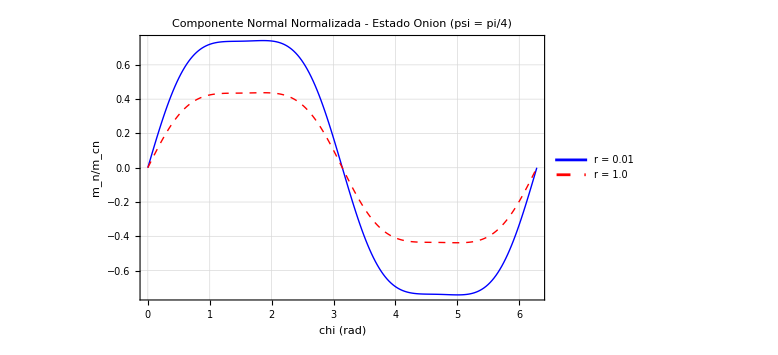

-Graphics-

Diagnostico:

m_cn (r=0.01): min = -0.741528, max = 0.741528

m_cn (r=1.0): min = -0.437449, max = 0.437449

```mathematica
(* =========================================*)(*ANALISE DA MAGNETIZACAO EM CONE-GAIDIDEI 2014*)(* =========================================*)(*PASSO 1:PARAMETRIZACAO DO CONE*)Print["PASSO 1: Parametrizacao do Cone (Eq. 9)"]

(*Coordenadas curvilineas*)
chi=Symbol["chi"]; (*angular:0 a 2pi*)
r=Symbol["r"];     (*radial:0 a w*)

(*Parametros do cone*)
R=1.0;             (*raio*)
psi=Pi/4;          (*angulo do cone*)

(*Parametrizacao:x+i*y=(R+r*cos(psi))*exp(i*chi),z=r*sin(psi)*)
xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi]
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi]
zCone[chi_,r_]:=r*Sin[psi]

(*Vetor posicao*)
rVec[chi_,r_]:={xCone[chi,r],yCone[chi,r],zCone[chi,r]}

Print["Vetor posicao r(chi,r) = ",rVec[chi,r]]

(* =========================================*)
(*PASSO 2:VETORES DA BASE TANGENTE*)
Print["\nPASSO 2: Vetores da Base Tangente"]

(*e_chi=dr/dchi*)
e1[chi_,r_]:=D[rVec[chi,r],chi]

(*e_r=dr/dr*)
e2[chi_,r_]:=D[rVec[chi,r],r]

Print["e_chi (e1) = ",e1[chi,r]//Simplify]
Print["e_r (e2) = ",e2[chi,r]//Simplify]

(*Componentes do tensor metrico*)
g11[chi_,r_]:=e1[chi,r].e1[chi,r]//Simplify
g22[chi_,r_]:=e2[chi,r].e2[chi,r]//Simplify
g12[chi_,r_]:=e1[chi,r].e2[chi,r]//Simplify

Print["g11 = ",g11[chi,r]]
Print["g22 = ",g22[chi,r]]
Print["g12 = ",g12[chi,r]," (deve ser 0 para base ortogonal)"]

(*Normalizar vetores da base*)
e1Norm[chi_,r_]:=e1[chi,r]/Sqrt[g11[chi,r]]
e2Norm[chi_,r_]:=e2[chi,r]/Sqrt[g22[chi,r]]

Print["e1 normalizado = ",e1Norm[chi,r]//Simplify]
Print["e2 normalizado = ",e2Norm[chi,r]//Simplify]

(* =========================================*)
(*PASSO 3:VETOR NORMAL*)
Print["\nPASSO 3: Vetor Normal"]

(*n=e1 x e2*)
nVec[chi_,r_]:=Cross[e1Norm[chi,r],e2Norm[chi,r]]//Simplify

Print["n = e1 x e2 = ",nVec[chi,r]]
Print["Verificar |n| = ",Norm[nVec[chi,r]]//Simplify," (deve ser 1)"]

(* =========================================*)
(*PASSO 4:SEGUNDA FORMA FUNDAMENTAL*)
Print["\nPASSO 4: Segunda Forma Fundamental (curvatura)"]

(*b_alphabeta=n.d(e_alpha)/d(xi_beta)*)
b11[chi_,r_]:=nVec[chi,r].D[e1[chi,r],chi]//Simplify
b12[chi_,r_]:=nVec[chi,r].D[e1[chi,r],r]//Simplify
b21[chi_,r_]:=nVec[chi,r].D[e2[chi,r],chi]//Simplify
b22[chi_,r_]:=nVec[chi,r].D[e2[chi,r],r]//Simplify

Print["b11 = ",b11[chi,r]]
Print["b12 = ",b12[chi,r]]
Print["b21 = ",b21[chi,r]]
Print["b22 = ",b22[chi,r]]

(*Matriz h_alphabeta=b_alphabeta/sqrt(g_alphaalpha*g_betabeta)*)
h11[chi_,r_]:=b11[chi,r]/Sqrt[g11[chi,r]*g11[chi,r]]//Simplify
h12[chi_,r_]:=b12[chi,r]/Sqrt[g11[chi,r]*g22[chi,r]]//Simplify
h22[chi_,r_]:=b22[chi,r]/Sqrt[g22[chi,r]*g22[chi,r]]//Simplify

Print["h11 = ",h11[chi,r]]
Print["h12 = ",h12[chi,r]]
Print["h22 = ",h22[chi,r]]

(*Curvatura de Gauss e curvatura media*)
K[chi_,r_]:=h11[chi,r]*h22[chi,r]-h12[chi,r]^2//Simplify
H[chi_,r_]:=(h11[chi,r]+h22[chi,r])/2//Simplify

Print["Curvatura de Gauss K = ",K[chi,r]]
Print["Curvatura Media H = ",H[chi,r]]

(* =========================================*)
(*PASSO 5:SPIN CONNECTION*)
Print["\nPASSO 5: Spin Connection Omega"]

(*varpi_1=e1.de2/dchi*)
varpi1[chi_,r_]:=e1Norm[chi,r].D[e2Norm[chi,r],chi]//Simplify

(*Omega=(varpi1/sqrt(g11),varpi2/sqrt(g22))*)
(*Para o cone,varpi2=0*)
Omega1[chi_,r_]:=varpi1[chi,r]/Sqrt[g11[chi,r]]//Simplify

Print["Omega_chi = varpi1/sqrt(g11) = ",Omega1[chi,r]]
Print["Omega_r = 0 (por simetria)"]

(* =========================================*)
(*PASSO 6:VETOR GAMMA (Eq.4)*)
Print["\nPASSO 6: Vetor Gamma(phi) - Eq. 4"]

(*Para o cone:Gamma=-e_chi*sin(psi)*cos(phi)/sqrt(g)*)
(*onde g=g11=(R+r*cos(psi))^2*)

phi=Symbol["phi"];
sqrtG[chi_,r_]:=Sqrt[g11[chi,r]]

GammaChi[phi_,chi_,r_]:=-Sin[psi]*Cos[phi]/sqrtG[chi,r]//Simplify
GammaR[phi_,chi_,r_]:=0

Print["Gamma_chi(phi) = ",GammaChi[phi,chi,r]]
Print["Gamma_r(phi) = ",GammaR[phi,chi,r]]

(* =========================================*)
(*PASSO 7:CAMPO EFETIVO F_t (Eq.5)*)
Print["\nPASSO 7: Campo Efetivo F_t(phi) - Eq. 5"]

(*F_t=div(Gamma)+(grad(phi)-Omega).(dGamma/dphi)*)

(*Divergencia de Gamma*)
divGamma[phi_,chi_,r_]:=Module[{sqrtg},sqrtg=Sqrt[g11[chi,r]*g22[chi,r]];
(1/sqrtg)*(D[GammaChi[phi,chi,r]*Sqrt[g11[chi,r]],chi]+D[GammaR[phi,chi,r]*Sqrt[g22[chi,r]],r])]//Simplify

(*grad(phi) em coordenadas curvilineas*)
gradPhiChi[chi_,r_]:=1/Sqrt[g11[chi,r]]
gradPhiR[chi_,r_]:=1/Sqrt[g22[chi,r]]

(*dGamma/dphi*)
dGammaDphi[phi_,chi_,r_]:=D[GammaChi[phi,chi,r],phi]//Simplify

(*F_t completo*)
Ft[phi_,dPhiDchi_,chi_,r_]:=Module[{term1,term2},term1=divGamma[phi,chi,r];
term2=(dPhiDchi*gradPhiChi[chi,r]-Omega1[chi,r])*dGammaDphi[phi,chi,r];
term1+term2]//Simplify

Print["F_t(phi, dphi/dchi) = "]
Print[Ft[phi,Symbol["dPhiDchi"],chi,r]]

(* =========================================*)
(*PASSO 8:SOLUCAO ONION phi(chi)*)
Print["\nPASSO 8: Solucao Onion phi_on(chi) - Eq. 11"]

(*Modulo k:2*k*K(k)=pi*sin(psi)*)
kEq=2*k*EllipticK[k^2]==Pi*Sin[psi];
kSol=FindRoot[kEq,{k,0.6}][[1,2]];

Print["Modulo k = ",kSol]
Print["Verificacao: 2*k*K(k^2) = ",2*kSol*EllipticK[kSol^2]//N]
Print["pi*sin(psi) = ",Pi*Sin[psi]//N]

(*Funcao phi_onion*)
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]

(* =========================================*)
(*PASSO 9:CALCULAR m_n/m_cn PARA PLOTAR*)
Print["\nPASSO 9: Calcular m_n/m_cn"]

(*Primeiro,criar funcao numerica para F_t*)
(*Simplificar F_t para o cone especificamente*)
FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Block[{gVal,result},gVal=(R+rVal*Cos[psi])^2;
result=Sin[psi]*Sin[phiVal]*(2*dPhiDchiVal-Cos[psi])/Sqrt[gVal];
result]

(*Valores numericos*)
nChi=200;
chiVals=Table[i,{i,0,2*Pi,2*Pi/nChi}];
rVals={0.01,1.0}; (*r=0 e r=R*)
sigma=0.15; (*parametro sigma*)

(*Calcular phi_onion para todos os chi*)
phiOnionVals=Table[phiOnion[chiVal],{chiVal,chiVals}];

(*Derivada numerica de phi*)
dPhiOnionVals=Table[If[i<Length[phiOnionVals],(phiOnionVals[[i+1]]-phiOnionVals[[i]])/(chiVals[[i+1]]-chiVals[[i]]),(phiOnionVals[[i]]-phiOnionVals[[i-1]])/(chiVals[[i]]-chiVals[[i-1]])],{i,1,Length[phiOnionVals]}];

(*Calcular m_cn para cada r*)
mcnData=Table[Table[{chiVals[[i]],R^2*FtCone[phiOnionVals[[i]],dPhiOnionVals[[i]],chiVals[[i]],rVal]},{i,1,Length[chiVals]}],{rVal,rVals}];

(* =========================================*)
(*PASSO 10:PLOTAR RESULTADOS*)
Print["\nPASSO 10: Plotagem"]

plot=ListLinePlot[mcnData,PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"r = 0.01","r = 1.0"},AxesLabel->{"chi (rad)","m_n/m_cn"},PlotLabel->"Componente Normal Normalizada - Estado Onion (psi = pi/4)",GridLines->Automatic,ImageSize->Large,Frame->True]

Print[plot]

(*Imprimir valores min/max para diagnostico*)
Print["\nDiagnostico:"]
Print["m_cn (r=0.01): min = ",Min[mcnData[[1,All,2]]],", max = ",Max[mcnData[[1,All,2]]]]
Print["m_cn (r=1.0): min = ",Min[mcnData[[2,All,2]]],", max = ",Max[mcnData[[2,All,2]]]]
```

```mathematica
(* =========================================*)(*ANALISE DA MAGNETIZACAO EM CONE-GAIDIDEI 2014*)(* =========================================*)(*PASSO 1:PARAMETRIZACAO DO CONE*)Print["PASSO 1: Parametrizacao do Cone (Eq. 9)"]

(*Coordenadas curvilineas*)
chi=Symbol["chi"]; (*angular:0 a 2pi*)
r=Symbol["r"];     (*radial:0 a w*)

(*Parametros do cone*)
R=1.0;             (*raio*)
psi=Pi/4;          (*angulo do cone*)

(*Parametrizacao:x+i*y=(R+r*cos(psi))*exp(i*chi),z=r*sin(psi)*)
xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi]
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi]
zCone[chi_,r_]:=r*Sin[psi]

(*Vetor posicao*)
rVec[chi_,r_]:={xCone[chi,r],yCone[chi,r],zCone[chi,r]}

Print["Vetor posicao r(chi,r) = ",rVec[chi,r]]

(* =========================================*)
(*PASSO 2:VETORES DA BASE TANGENTE*)
Print["\nPASSO 2: Vetores da Base Tangente"]

(*e_chi=dr/dchi*)
e1[chi_,r_]:=D[rVec[chi,r],chi]

(*e_r=dr/dr*)
e2[chi_,r_]:=D[rVec[chi,r],r]

Print["e_chi (e1) = ",e1[chi,r]//Simplify]
Print["e_r (e2) = ",e2[chi,r]//Simplify]

(*Componentes do tensor metrico*)
g11[chi_,r_]:=e1[chi,r].e1[chi,r]//Simplify
g22[chi_,r_]:=e2[chi,r].e2[chi,r]//Simplify
g12[chi_,r_]:=e1[chi,r].e2[chi,r]//Simplify

Print["g11 = ",g11[chi,r]]
Print["g22 = ",g22[chi,r]]
Print["g12 = ",g12[chi,r]," (deve ser 0 para base ortogonal)"]

(*Normalizar vetores da base*)
e1Norm[chi_,r_]:=e1[chi,r]/Sqrt[g11[chi,r]]
e2Norm[chi_,r_]:=e2[chi,r]/Sqrt[g22[chi,r]]

Print["e1 normalizado = ",e1Norm[chi,r]//Simplify]
Print["e2 normalizado = ",e2Norm[chi,r]//Simplify]

(* =========================================*)
(*PASSO 3:VETOR NORMAL*)
Print["\nPASSO 3: Vetor Normal"]

(*n=e1 x e2*)
nVec[chi_,r_]:=Cross[e1Norm[chi,r],e2Norm[chi,r]]//Simplify

Print["n = e1 x e2 = ",nVec[chi,r]]
Print["Verificar |n| = ",Norm[nVec[chi,r]]//Simplify," (deve ser 1)"]

(* =========================================*)
(*PASSO 4:SEGUNDA FORMA FUNDAMENTAL*)
Print["\nPASSO 4: Segunda Forma Fundamental (curvatura)"]

(*b_alphabeta=n.d(e_alpha)/d(xi_beta)*)
b11[chi_,r_]:=nVec[chi,r].D[e1[chi,r],chi]//Simplify
b12[chi_,r_]:=nVec[chi,r].D[e1[chi,r],r]//Simplify
b21[chi_,r_]:=nVec[chi,r].D[e2[chi,r],chi]//Simplify
b22[chi_,r_]:=nVec[chi,r].D[e2[chi,r],r]//Simplify

Print["b11 = ",b11[chi,r]]
Print["b12 = ",b12[chi,r]]
Print["b21 = ",b21[chi,r]]
Print["b22 = ",b22[chi,r]]

(*Matriz h_alphabeta=b_alphabeta/sqrt(g_alphaalpha*g_betabeta)*)
h11[chi_,r_]:=b11[chi,r]/Sqrt[g11[chi,r]*g11[chi,r]]//Simplify
h12[chi_,r_]:=b12[chi,r]/Sqrt[g11[chi,r]*g22[chi,r]]//Simplify
h22[chi_,r_]:=b22[chi,r]/Sqrt[g22[chi,r]*g22[chi,r]]//Simplify

Print["h11 = ",h11[chi,r]]
Print["h12 = ",h12[chi,r]]
Print["h22 = ",h22[chi,r]]

(*Curvatura de Gauss e curvatura media*)
K[chi_,r_]:=h11[chi,r]*h22[chi,r]-h12[chi,r]^2//Simplify
H[chi_,r_]:=(h11[chi,r]+h22[chi,r])/2//Simplify

Print["Curvatura de Gauss K = ",K[chi,r]]
Print["Curvatura Media H = ",H[chi,r]]

(* =========================================*)
(*PASSO 5:SPIN CONNECTION*)
Print["\nPASSO 5: Spin Connection Omega"]

(*varpi_1=e1.de2/dchi*)
varpi1[chi_,r_]:=e1Norm[chi,r].D[e2Norm[chi,r],chi]//Simplify

(*Omega=(varpi1/sqrt(g11),varpi2/sqrt(g22))*)
(*Para o cone,varpi2=0*)
Omega1[chi_,r_]:=varpi1[chi,r]/Sqrt[g11[chi,r]]//Simplify

Print["Omega_chi = varpi1/sqrt(g11) = ",Omega1[chi,r]]
Print["Omega_r = 0 (por simetria)"]

(* =========================================*)
(*PASSO 6:VETOR GAMMA (Eq.4)*)
Print["\nPASSO 6: Vetor Gamma(phi) - Eq. 4"]

(*Para o cone:Gamma=-e_chi*sin(psi)*cos(phi)/sqrt(g)*)
(*onde g=g11=(R+r*cos(psi))^2*)

phi=Symbol["phi"];
sqrtG[chi_,r_]:=Sqrt[g11[chi,r]]

GammaChi[phi_,chi_,r_]:=-Sin[psi]*Cos[phi]/sqrtG[chi,r]//Simplify
GammaR[phi_,chi_,r_]:=0

Print["Gamma_chi(phi) = ",GammaChi[phi,chi,r]]
Print["Gamma_r(phi) = ",GammaR[phi,chi,r]]

(* =========================================*)
(*PASSO 7:CAMPO EFETIVO F_t (Eq.5)*)
Print["\nPASSO 7: Campo Efetivo F_t(phi) - Eq. 5"]

(*F_t=div(Gamma)+(grad(phi)-Omega).(dGamma/dphi)*)

(*Divergencia de Gamma*)
divGamma[phi_,chi_,r_]:=Module[{sqrtg},sqrtg=Sqrt[g11[chi,r]*g22[chi,r]];
(1/sqrtg)*(D[GammaChi[phi,chi,r]*Sqrt[g11[chi,r]],chi]+D[GammaR[phi,chi,r]*Sqrt[g22[chi,r]],r])]//Simplify

(*grad(phi) em coordenadas curvilineas*)
gradPhiChi[chi_,r_]:=1/Sqrt[g11[chi,r]]
gradPhiR[chi_,r_]:=1/Sqrt[g22[chi,r]]

(*dGamma/dphi*)
dGammaDphi[phi_,chi_,r_]:=D[GammaChi[phi,chi,r],phi]//Simplify

(*F_t completo*)
Ft[phi_,dPhiDchi_,chi_,r_]:=Module[{term1,term2},term1=divGamma[phi,chi,r];
term2=(dPhiDchi*gradPhiChi[chi,r]-Omega1[chi,r])*dGammaDphi[phi,chi,r];
term1+term2]//Simplify

Print["F_t(phi, dphi/dchi) = "]
Print[Ft[phi,Symbol["dPhiDchi"],chi,r]]

(* =========================================*)
(*PASSO 8:SOLUCAO ONION phi(chi)*)
Print["\nPASSO 8: Solucao Onion phi_on(chi) - Eq. 11"]

(*Modulo k:2*k*K(k)=pi*sin(psi)*)
kEq=2*k*EllipticK[k^2]==Pi*Sin[psi];
kSol=FindRoot[kEq,{k,0.6}][[1,2]];

Print["Modulo k = ",kSol]
Print["Verificacao: 2*k*K(k^2) = ",2*kSol*EllipticK[kSol^2]//N]
Print["pi*sin(psi) = ",Pi*Sin[psi]//N]

(*Funcao phi_onion*)
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]

(* =========================================*)
(*PASSO 9:CALCULAR m_n/m_cn PARA PLOTAR*)
Print["\nPASSO 9: Calcular m_n/m_cn"]

(*Primeiro,criar funcao numerica para F_t*)
(*Simplificar F_t para o cone especificamente*)
FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Block[{gVal,result},gVal=(R+rVal*Cos[psi])^2;
result=Sin[psi]*Sin[phiVal]*(2*dPhiDchiVal-Cos[psi])/Sqrt[gVal];
result]

(*Valores numericos*)
nChi=200;
chiVals=Table[i,{i,0,2*Pi,2*Pi/nChi}];
rVals={0.01,1.0}; (*r=0 e r=R*)
sigma=0.15; (*parametro sigma*)

(*Calcular phi_onion para todos os chi*)
phiOnionVals=Table[phiOnion[chiVal],{chiVal,chiVals}];

(*Derivada numerica de phi*)
dPhiOnionVals=Table[If[i<Length[phiOnionVals],(phiOnionVals[[i+1]]-phiOnionVals[[i]])/(chiVals[[i+1]]-chiVals[[i]]),(phiOnionVals[[i]]-phiOnionVals[[i-1]])/(chiVals[[i]]-chiVals[[i-1]])],{i,1,Length[phiOnionVals]}];

(*Calcular m_cn para cada r*)
mcnData=Table[Table[{chiVals[[i]],R^2*FtCone[phiOnionVals[[i]],dPhiOnionVals[[i]],chiVals[[i]],rVal]},{i,1,Length[chiVals]}],{rVal,rVals}];

(* =========================================*)
(*PASSO 10:PLOTAR RESULTADOS*)
Print["\nPASSO 10: Plotagem"]

plot=ListLinePlot[mcnData,PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"r = 0.01","r = 1.0"},AxesLabel->{"chi (rad)","m_n/m_cn"},PlotLabel->"Componente Normal Normalizada - Estado Onion (psi = pi/4)",GridLines->Automatic,ImageSize->Large,Frame->True]

Print[plot]

(*Imprimir valores min/max para diagnostico*)
Print["\nDiagnostico:"]
Print["m_cn (r=0.01): min = ",Min[mcnData[[1,All,2]]],", max = ",Max[mcnData[[1,All,2]]]]
Print["m_cn (r=1.0): min = ",Min[mcnData[[2,All,2]]],", max = ",Max[mcnData[[2,All,2]]]]
```

PASSO 1: Parametrizacao do Cone (Eq. 9)

Vetor posicao r(chi,r) = {(1.+r/(√2)) Cos[chi],(1.+r/(√2)) Sin[chi],r/(√2)}

PASSO 2: Vetores da Base Tangente

e_chi (e1) = {(-1.-0.707107 r) Sin[chi],(1.+0.707107 r) Cos[chi],0}

e_r (e2) = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

g11 = 0.5 (2.+2.82843 r+r^2)

g22 = 1

g12 = 0 (deve ser 0 para base ortogonal)

e1 normalizado = {((-1.41421-1. r) Sin[chi])/(√(2.+2.82843 r+r^2)),((1.41421+1. r) Cos[chi])/(√(2.+2.82843 r+r^2)),0.}

e2 normalizado = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

PASSO 3: Vetor Normal

n = e1 x e2 = {((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2)),((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2)),(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))}

Verificar |n| = √(Abs[(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2))]^2) (deve ser 1)

PASSO 4: Segunda Forma Fundamental (curvatura)

b11 = -0.5 √(2.+2.82843 r+r^2)

b12 = 0

b21 = 0

b22 = 0

h11 = -(1. √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

h12 = 0.

h22 = 0

Curvatura de Gauss K = 0

Curvatura Media H = -(0.5 √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

PASSO 5: Spin Connection Omega

Omega_chi = varpi1/sqrt(g11) = (1.41421+1. r)/(2.+2.82843 r+r^2)

Omega_r = 0 (por simetria)

PASSO 6: Vetor Gamma(phi) - Eq. 4

Gamma_chi(phi) = -(1. Cos[phi])/(√(2.+2.82843 r+r^2))

Gamma_r(phi) = 0

PASSO 7: Campo Efetivo F_t(phi) - Eq. 5

F_t(phi, dphi/dchi) =

-(1. (dPhiDchi (-2.82843-4. r-1.41421 r^2)+1. (1.41421+1. r) √(2.+2.82843 r+r^2)) Sin[phi])/((2.+2.82843 r+r^2)^2)

PASSO 8: Solucao Onion phi_on(chi) - Eq. 11

Modulo k = 0.626647

Verificacao: 2*k*K(k^2) = 2.22144

pi*sin(psi) = 2.22144

PASSO 9: Calcular m_n/m_cn

PASSO 10: Plotagem

-Graphics-

-Graphics-

Diagnostico:

m_cn (r=0.01): min = -0.741528, max = 0.741528

m_cn (r=1.0): min = -0.437449, max = 0.437449

Processando Painel B: ψ = 0...

Processando Painel C: ψ = π/4...

Processando Painel D: mn(χ)...

Processando Painel E: Plano de Corte...

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL D: mn(χ) ===

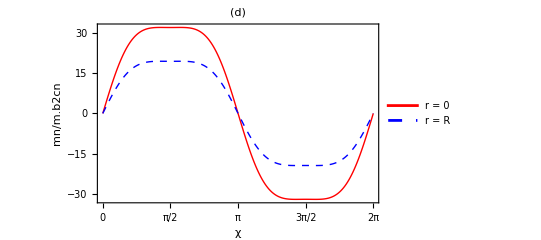

=== PAINEL E: Plano de Corte ===

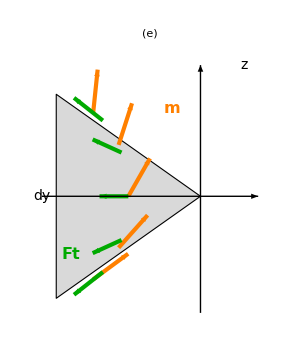

=== FIGURA 1 COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Sin[psi]*Sin[phiVal]*(2*dPhiDchiVal-Cos[psi])/Sqrt[(R+rVal*Cos[psi])^2];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
R^2*FtCone[phiVal,dPhiVal,chiVal,rVal]/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e vetor*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.1;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Thickness[0.006],Arrowheads[0.025],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["Processando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Thickness[0.006],Arrowheads[0.025],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)*)
(* =========================================*)

Print["Processando Painel D: mn(χ)..."];

mnDataD={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

plotD=ListLinePlot[mnDataD,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"r = 0","r = R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d)",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},All},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->400,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["Processando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Superfície do cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;(*ângulo típico*)angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*EXIBIR RESULTADOS*)
(* =========================================*)

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL D: mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo*)
finalFig=GraphicsGrid[{{plotB,plotC},{plotD,plotE}},ImageSize->850,Spacings->{40,40}];

Print["\n=== FIGURA 1 COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

Processando Painel C: ψ = π/4...

Processando Painel D: mn(χ)...

DEBUG - Teste phi_onion:

phi(0) = 0.

phi(π/2) = 1.5708

phi(π) = 3.14159

dphi/dchi(0) = 1.1284

dphi/dchi(π/2) = 0.879363

Ft(π/2, r=0.5) = 0.549374

DEBUG - Valores de mn:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

Processando Painel E: Plano de Corte...

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL D: mn(χ) ===

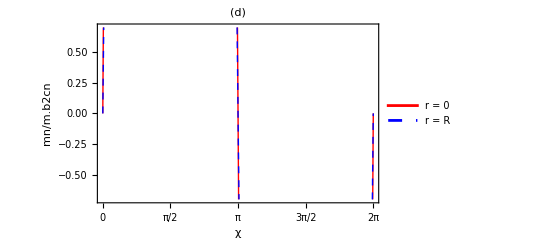

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA 1 COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
(*mn=R^2*Ft,normalizado por mcn*)R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
(*Retornar pontos para Arrow*){startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["Processando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)*)
(* =========================================*)

Print["Processando Painel D: mn(χ)..."];

(*Debug:Testar phi e derivada*)
Print["DEBUG - Teste phi_onion:"];
Print["  phi(0) = ",phiC[0]];
Print["  phi(π/2) = ",phiC[Pi/2]];
Print["  phi(π) = ",phiC[Pi]];
Print["  dphi/dchi(0) = ",Derivative[1][phiC][0]];
Print["  dphi/dchi(π/2) = ",Derivative[1][phiC][Pi/2]];

(*Testar Ft diretamente*)
testChi=Pi/2;
testR=0.5;
testPhi=phiC[testChi];
testDPhi=Derivative[1][phiC][testChi];
Print["  Ft(π/2, r=0.5) = ",Sin[Pi/4]*Sin[testPhi]*(2*testDPhi-Cos[Pi/4])/Sqrt[(R+testR*Cos[Pi/4])^2]];

mnDataD={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - Valores de mn:"];
Print["  r=0.05: Min = ",Min[mnDataD[[1,All,2]]],", Max = ",Max[mnDataD[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataD[[2,All,2]]],", Max = ",Max[mnDataD[[2,All,2]]]];

plotD=ListLinePlot[mnDataD,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"r = 0","r = R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d)",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->400,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["Processando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Superfície do cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;(*ângulo típico*)angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*EXIBIR RESULTADOS*)
(* =========================================*)

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL D: mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo*)
finalFig=GraphicsGrid[{{plotB,plotC},{plotD,plotE}},ImageSize->850,Spacings->{40,40}];

Print["\n=== FIGURA 1 COMPLETA ==="];
Print[finalFig];
```